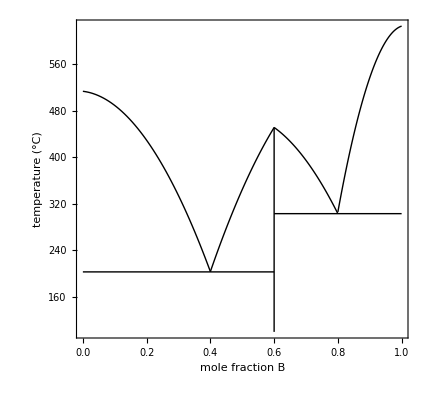

```mathematica
Module[{f1,f2,f3,f4,f5,f6},
f1=203;f2=303;
f3[x_]:=-1769*x^2-66.42*x+513.1;
f4[x_]:=-1718*x^2+2955*x-703.6;
f5[x_]:=-1756*x^2+1718*x+52.36;
f6[x_]:=-7097*x^2+14370*x-6648;

Show[
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},{f3[x],{0,0.4}},{f4[x],{0.4,0.6}},{f5[x],{0.6,0.8}},{f6[x],{0.8,1}}},
Graphics@{Thick,Line[{{0.6,100},{0.6,f5[0.6]}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full]
]
```

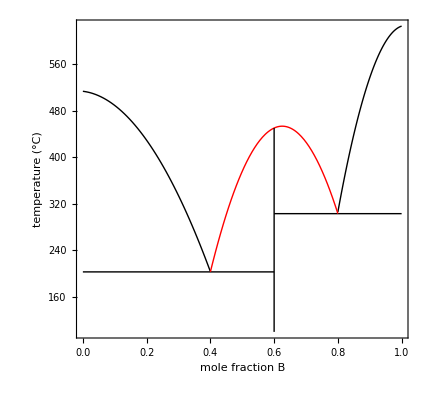

```mathematica
Module[{f1,f2,f3,f4,f5,f6,y,s1,s2,s3},
f1=203;f2=303;
f3[x_]:=-1769*x^2-66.42*x+513.1;
f4[x_]:=-1718*x^2+2955*x-703.6;
f5[x_]:=-1756*x^2+1718*x+52.36;
f6[x_]:=-7097*x^2+14370*x-6648;

y[x_]:=a*x^2+b*x+c;
s1=Quiet@Flatten@Solve[y[0.4]==f1∧y[0.48]==f4[0.5]∧y[0.6]==f5[0.6],{a,b,c}];
s2=Quiet@Flatten@Solve[y[0.6]==f4[0.6]∧y[0.72]==f5[0.7]∧y[0.8]==f2,{a,b,c}];
s3=Quiet@Flatten@Solve[y[0.4]==f1∧y[0.6]==450∧y[0.8]==f2,{a,b,c}];

Show[
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},{f3[x],{0,0.4}},(*{f4[x],{0.4,0.6}},{f5[x],{0.6,0.8}},*){f6[x],{0.8,1}}},

(*Plot[y[x]/.s1,{x,0.4,0.6},PlotStyle->{Thick,Black}],
Plot[y[x]/.s2,{x,0.6,0.8},PlotStyle->{Thick,Black}],*)
Plot[y[x]/.s3,{x,0.4,0.8},PlotStyle->{Thick,Red}],

Graphics@{Thick,Line[{{0.6,100},{0.6,450}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full]
]
```

```mathematica
Module[{f1,f2,f3,f4,f5,f6,y,s1,s2,s3},
f1=203;f2=303;
f3[x_]:=-1769*x^2-66.42*x+513.1;
f4[x_]:=-1718*x^2+2955*x-703.6;
f5[x_]:=-1756*x^2+1718*x+52.36;
f6[x_]:=-7097*x^2+14370*x-6648;

y[x_]:=a*x^2+b*x+c;
s1=Quiet@Flatten@Solve[y[0.35]==f1∧y[0.6]==450∧y[0.8]==f2,{a,b,c}];
s2=Quiet@Flatten@Solve[y[0]==515∧y[0.2]==400∧y[0.35]==f1,{a,b,c}];

Show[
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},(*{f3[x],{0,0.35}},{f4[x],{0.35,0.6}},{f5[x],{0.6,0.8}},*){f6[x],{0.8,1}}},

Plot[y[x]/.s1,{x,0.35,0.8},PlotStyle->{Thick,Red}],
Plot[y[x]/.s2,{x,0,0.35},PlotStyle->{Thick,Blue}],

Graphics@{Thick,Line[{{0.6,100},{0.6,450}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full];
y[x]/.s1
]
```

-946.867+4625.44 x-3828.89 x^2

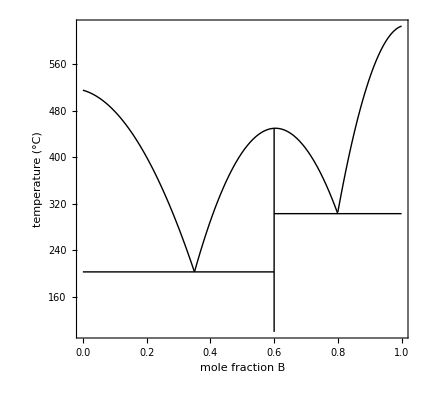

```mathematica
Module[{f1,f2,f3,f4,f5},
f1=203;f2=303;
f3[x_]:=-2110*x^2-153*x+515;
f4[x_]:=-3829*x^2+4625*x-947;
f5[x_]:=-7097*x^2+14370*x-6648;

Show[
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},{f3[x],{0,0.35}},{f4[x],{0.35,0.8}},{f5[x],{0.8,1}}},
Graphics@{Thick,Line[{{0.6,100},{0.6,450}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full]
]
```

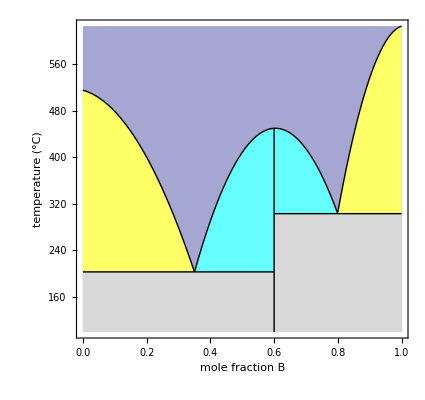

```mathematica
Module[{f1,f2,f3,f4,f5},
f1=203;f2=303;
f3[x_]:=-2110*x^2-153*x+515;
f4[x_]:=-3829*x^2+4625*x-947;
f5[x_]:=-7097*x^2+14370*x-6648;

Show[
Graphics@{Directive[Darker[Blue,0.5],Opacity@0.35],Rectangle[{0,100},{1,625}]},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->None,Filling->#3,FillingStyle->#4]&@@@{
{f1,{0,0.6},100,GrayLevel@0.85},
{f2,{0.6,1},100,GrayLevel@0.85},
{f3[x],{0,0.35},f1,RGBColor[1,1,0.4]},
{f4[x],{0.35,0.6},f1,RGBColor[0.4,1,1]},
{f4[x],{0.6,0.8},f2,RGBColor[0.4,1,1]},
{f5[x],{0.8,1},f2,RGBColor[1,1,0.4]}},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},{f3[x],{0,0.35}},{f4[x],{0.35,0.8}},{f5[x],{0.8,1}}},
Graphics@{Thick,Line[{{0.6,100},{0.6,450}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full]
]
```